```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Fine soil data *)
fsSieve={{10.000,1},{5.000,1},{2.360,1},{2.000,1},{1.180,0.99},{0.600,0.96},{0.425,0.90},{0.300,0.79},{0.180,0.52},{0.075,0.081},{0.050,0}};
```

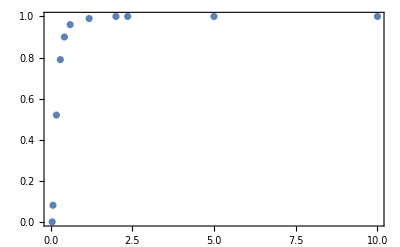

```mathematica
ListPlot[fsSieve,PlotRange->All,Frame->True]
```

```mathematica
CDFfit=Normal[NonlinearModelFit[fsSieve,CDF[LogNormalDistribution[μ,σ],x][[1,1,1]],{μ,σ},x]]
```

1/2 Erfc[1.10179 (-1.72436-Log[x])]

```mathematica
CDF[LogNormalDistribution[μ,σ],x][[1,1,1]]
```

1/2 Erfc[(μ-Log[x])/(√2 σ)]

```mathematica
s=1/(CDFfit[[2,1,1]] √2)
u=CDFfit[[2,1,1]]*CDFfit[[2,1,2,1]]*s √2
```

0.64178

-1.72436

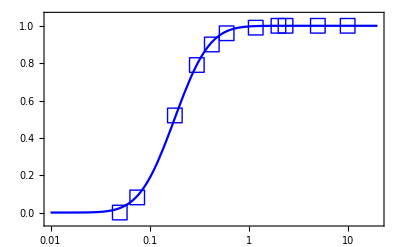

```mathematica
Show[{
ListLogLinearPlot[fsSieve,PlotRange->{{0.01,20},{-0.05,1.05}},Frame->True,FrameStyle->Directive[{15,Black,Thickness[0.00275]}],PlotStyle->Blue,PlotMarkers->{"□",15}],
LogLinearPlot[1/2 Erfc[(u-Log[x])/(√2 s)],{x,0.01,20},PlotStyle->Blue]
}]
```

```mathematica
Mean[LogNormalDistribution[u,s]]
StandardDeviation[LogNormalDistribution[u,s]]
```

0.219058

0.156386

```mathematica
(* Coarse soil data *)
csSieve={{0.075,0},{0.180,0},{0.25,0},{0.355,0.027565953},{0.425,0.063044414},{0.5,0.109733818},{0.6,0.153517605},{0.71,0.273533318},{0.85,0.865830314},{1,0.99986906},{2.000,1},{2.360,1}};
```

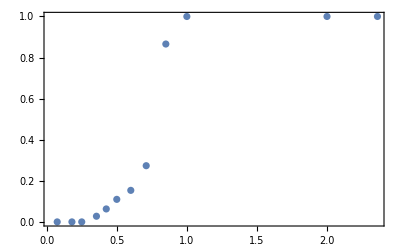

```mathematica
ListPlot[csSieve,PlotRange->All,Frame->True]
```

```mathematica
CDFfit=Normal[NonlinearModelFit[csSieve,CDF[LogNormalDistribution[μ,σ],x][[1,1,1]],{μ,σ},x]]
```

1/2 Erfc[5.5387 (-0.284984-Log[x])]

```mathematica
CDF[LogNormalDistribution[μ,σ],x][[1,1,1]]
```

1/2 Erfc[(μ-Log[x])/(√2 σ)]

```mathematica
s=1/(CDFfit[[2,1,1]] √2)
u=CDFfit[[2,1,1]]*CDFfit[[2,1,2,1]]*s √2
```

0.127666

-0.284984

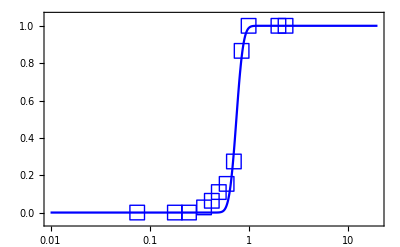

```mathematica
Show[{
ListLogLinearPlot[csSieve,PlotRange->{{0.01,20},{-0.05,1.05}},Frame->True,FrameStyle->Directive[{15,Black,Thickness[0.00275]}],PlotStyle->Blue,PlotMarkers->{"□",15}],
LogLinearPlot[1/2 Erfc[(u-Log[x])/(√2 s)],{x,0.01,20},PlotStyle->Blue]
}]
```

```mathematica
Mean[LogNormalDistribution[u,s]]
StandardDeviation[LogNormalDistribution[u,s]]
```

0.75818

0.0971899